## Investigations in pr(Λ_b|c_2,... ,c_k)

## The pdf and coefficients

Given our assumption that only c_2-c_k contribute to our determination of Λ_b, the posterior for set C_ϵ turns out to be

```mathematica
cksq[bvec_,Lb_,k_]:=Sum[bvec[[i]]^2 Lb^(2i),{i,1,k}]
Lbprior[Lb_]:=1/Lb
prLb[Lb_,bvec_,k_]:=Lbprior[Lb](Lb^(k+2)/cksq[bvec,Lb,k])^((k-1)/2)
```

To convert between the (assumed natural) c coefficient vector and the b coefficient vector (which doesn’t know about Λ_b), define the following

```mathematica
cvtobv[cv_,Lb_]:=Table[cv[[i]]/Lb^i,{i,1,Length[cv]}]
bvtocv[bv_,Lb_]:=Table[bv[[i]]*Lb^i,{i,1,Length[bv]}]
```

We assume that the lists start with c_1.

## What definition of “natural” does the posterior find?

It looks plausible that the Λ_b pdf determines the optimal Λ_b as if it were balancing c_2-c_kon a seesaw, with their positions along the seesaw set by their subscripts, with the fulcrum placed at the center, and their masses set by their magnitudes.

```mathematica
seesawbalance[bvec_,Lb_,power_]:=Module[{fulcrum,kk, klower, kupper,cveclower,cvecupper,ii},
(* Return difference of "torque" on each side of coefficient seesaw.
Power is the exponent of the "distances".
Power=1 is the true torque equation, while power=0 removes distance dependence. *)
kk=Length[bvec];
fulcrum=(Length[bvec]+2)/2;
cveclower={};
cvecupper={};
For[ii=2,ii≤Length[bvec],ii++,
If[ii-fulcrum<0,
AppendTo[cveclower,bvec[[ii]] Lb^ii],ii];
If[ii-fulcrum>0,
AppendTo[cvecupper,bvec[[ii]] Lb^ii],ii];
];
cveclower=Abs[Reverse[cveclower]];
cvecupper=Abs[cvecupper];
(*Print[cveclower//N];
Print[cvecupper//N];*)
Sum[(cveclower[[i]]-cvecupper[[i]])*(i-Mod[fulcrum,1])^power,{i,1,Length[cveclower]}
]
]
```

## Tests

```mathematica
Lbtestfunc[cvec_,Ltrue_,pow_]:=Module[{k,bv,Lmax,prLbmax,Lseesaw,cvmax,pplottrue,pplotpost,pplotseesaw1,ell,logplt,LbPlot},
Print["Testing c vector ", N[cvec,3]," with Λ_b=",Ltrue,"."];
Print["The seesaw balance uses a distance power of ", pow,"."];
(* Initialize relevant variables *)
k=Length[cvec];
bv=cvtobv[cvec,Ltrue];
Lmax=FindArgMax[Log[prLb[ell,bv,k]],{ell,Ltrue},PrecisionGoal->Infinity,WorkingPrecision->100][[1]];
prLbmax=prLb[Lmax,bv,k];
Lseesaw=FindArgMin[{seesawbalance[bv,ell,pow]^2,ell>Ltrue/3},{ell,2*Ltrue},
(*{ell},*)
PrecisionGoal->Infinity,WorkingPrecision->100][[1]];
(*Lseesaw=NArgMin[{seesawbalance[bv,ell,pow],ell>Ltrue/10},ell,PrecisionGoal->Infinity];*)
(*Lseesaw=ell/.FindRoot[{seesawbalance[bv,ell,pow]==0,ell>Ltrue/10},{ell,Ltrue+10},PrecisionGoal->Infinity][[1]];*)
cvmax=bvtocv[bv,Lmax];
Print["b vector: ", N[bv,3]];
Print["Posterior maximized by Λ_b = ", N[Lmax,4]];
Print["Seesaw equalized by Λ_b = ", N[Lseesaw,4]];

(* Setup plots *)
LbPlot=Plot[prLb[Lb,bv,k]/prLbmax,{Lb,0,2*Ltrue},PlotRange->All,PlotLabel->"pr(Λ_b|c_2,...,c_k)"];
logplt=LogPlot[seesawbalance[bv,Lb,pow]^2,{Lb,0,2*Ltrue},PlotRange->All,PlotLabel->"Log of squared seesaw balance",AxesLabel->{"Λ_b",""}];
pplotseesaw1=PolarPlot[Lseesaw/Cos[t],{t,0,ArcTan[(prLb[Lseesaw,bv,k]/prLbmax)/Lseesaw]},PlotStyle->{Gray,Dashed},PlotLegends->{"Λ_b=Λ_seesaw"}];
pplottrue=PolarPlot[Ltrue/Cos[t],{t,0,ArcTan[(prLb[Ltrue,bv,k]/prLbmax)/Ltrue]},PlotStyle->{Red,Dotted},PlotLegends->{"Λ_b=Λ_true"}];
pplotpost=PolarPlot[Lmax/Cos[t],{t,0,ArcTan[(prLb[Lmax,bv,k]/prLbmax)/Lmax]},PlotStyle->{Blue,DotDashed},PlotLegends->{"Λ_b=Λ_max"}];

(* Output plots in separate cells *)
CellPrint[{
Cell[BoxData[ToBoxes[Show[LbPlot,pplotseesaw1,pplottrue,pplotpost]]],"Output"],
Cell[BoxData[ToBoxes[Show[logplt]]],"Output"]
}
]
]
```

```mathematica
□Lbtesthistfunc[cvectable_,Ltrue_,pow_]:=Module[{ii,k,bvtable,Lmaxvec,Lseesawvec},
k=Length[cvectable[[1]]];
bvtable=Table[cvtobv[cvectable[[ii]],Ltrue],{ii,1,Length[cvectable]}];
Lmaxvec=Table[
FindArgMax[Log[prLb[ell,bvtable[[ii]],k]],{ell,Ltrue},PrecisionGoal->Infinity,WorkingPrecision->100][[1]],
{ii,1,Length[bvtable]}
];
Lseesawvec=Table[
FindArgMin[{seesawbalance[bvtable[[ii]],ell,pow]^2,ell>Ltrue/10},{ell,Ltrue+10},PrecisionGoal->Infinity,WorkingPrecision->100][[1]],
{ii,1,Length[bvtable]}
];
Histogram[Lmaxvec-Lseesawvec,PlotLabel->"Λ_post-Λ_seesaw"]
]
```

### Test with all relevant coefficients set to one.

Testing c vector {0,1.,1.,1.,1.,1.,1.,1.,1.,1.} with Λ_b=100.

The seesaw balance uses a distance power of 1.

b vector: {0,0.0001,1.×10^-6,1.×10^-8,1.×10^-10,1.×10^-12,1.×10^-14,1.×10^-16,1.×10^-18,1.×10^-20}

Posterior maximized by Λ_b = 99.17

Seesaw equalized by Λ_b = 100.

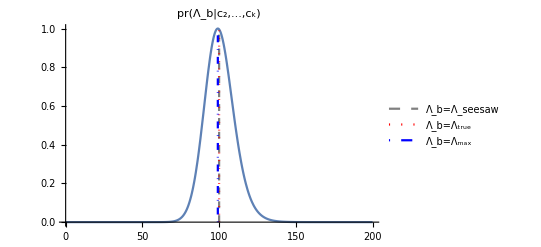

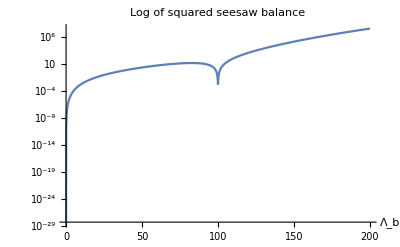

```mathematica
k=10;
cv=Join[{0,1},Table[1,k-3],{1}];
Ltrue=100;
Lbtestfunc[cv,Ltrue,1]
```

### Now with random reals

Testing c vector {0,9.48,6.74,1.15,-8.35,3.27,8.99,-4.27,6.12,-6.93} with Λ_b=100.

The seesaw balance uses a distance power of 1.

b vector: {0,0.000948,6.74×10^-6,1.15×10^-8,-8.35×10^-10,3.27×10^-12,8.99×10^-14,-4.27×10^-16,6.12×10^-18,-6.93×10^-20}

Posterior maximized by Λ_b = 101.6

Seesaw equalized by Λ_b = 101.3

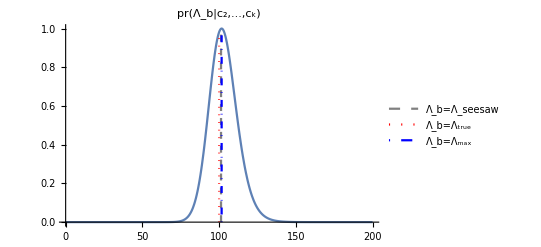

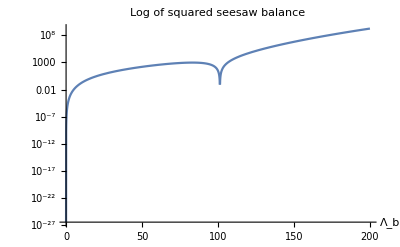

```mathematica
k=10;
cv=Join[{0},RandomReal[{-10,10},k-1,WorkingPrecision->100]];
Ltrue=100;
Lbtestfunc[cv,Ltrue,1]
```

### Let the c_ns be normally distributed

Testing c vector {0,-2.25,2.47,-4.63,-4.46,2.54,-1.33,-0.555,4.56,-7.18} with Λ_b=100.

The seesaw balance uses a distance power of 1.

b vector: {0,-0.000225,2.47×10^-6,-4.63×10^-8,-4.46×10^-10,2.54×10^-12,-1.33×10^-14,-5.55×10^-17,4.56×10^-18,-7.18×10^-20}

Posterior maximized by Λ_b = 91.69

Seesaw equalized by Λ_b = 93.84

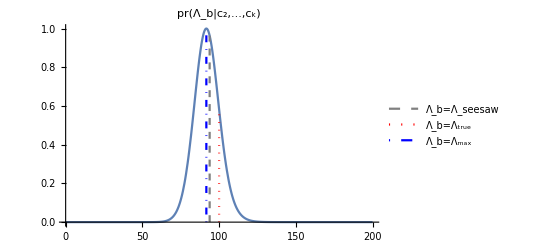

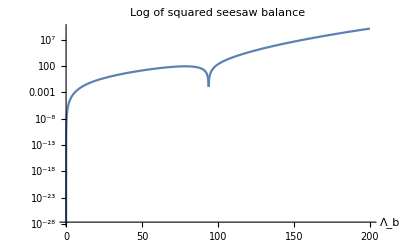

```mathematica
k=10;
cv=Join[{0},RandomVariate[NormalDistribution[0,5],k-1,WorkingPrecision->100]];
Ltrue=100;
Lbtestfunc[cv,Ltrue,1]
```

### Compare Λ_b estimator from posterior with seesaw method

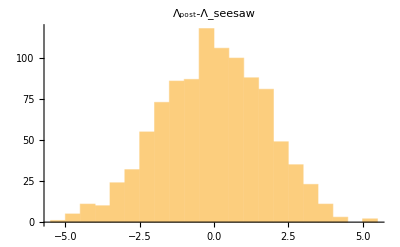

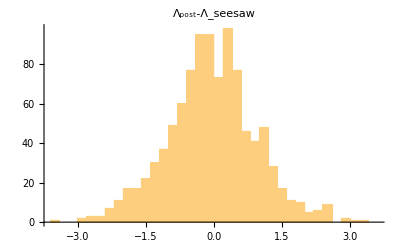

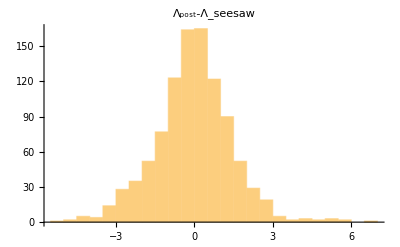

```mathematica
k=20;
n=1000;
rvs=RandomVariate[NormalDistribution[0,5],{n,k-1},WorkingPrecision->100];
cv=Table[Prepend[rvs[[i]],0],{i,1,n}];
Ltrue=100;
seesawpower=0;
Lbtesthistfunc[cv,Ltrue,seesawpower]
seesawpower=1;
Lbtesthistfunc[cv,Ltrue,seesawpower]
seesawpower=2;
Lbtesthistfunc[cv,Ltrue,seesawpower]
```

## Conclusions

It looks like the seesaw balance theory does tend to follow the maximum of the the posterior so long as there is sufficient statistics, but there is still variability. It does not show any trend towards, say, the median, or any other value relative to the distribution as far as I can tell. Treating the coefficients as if they were balancing on a seesaw, that is, weighting the coefficients linearly with distance from the fulcrum, seems to minimize the variance from the posterior maximum, as opposed to no weighting, or squared weighting.